```mathematica
(b) Decay Model (exponential case only)
Exponential Decay:
If a function x(t) decreses continuously at a rate k>0, its differential equation is given by
dx/dy = -kx, k>0
then x(t) has the form
x(t) = Subscript[x, o] e^-kt
where Subscript[x, o] is the initial amout x(0). In this case, the quantity x(t) is said to exhibit exponential decay, and k is the decay rate.
```

```mathematica
Example - 4
Suppose that a certain radioactive element has an annual decay rate of 10% . Starting with a 200gram sample of the element, how many grams will be left in 3 years ?
```

```mathematica
Subscript[x, o] = 200 , k=10%=.1 , x[t] in 3 years = ?
```

```mathematica
Sol= DSolve[x'[t]==-k*x[t],x[t],t]
```

{{x[t]→ⅇ^(-k t) C[1]}}

```mathematica
Sol1=Evaluate[x[t]/.Sol[[1]]/.{k-> .1,C[1]-> 200}]
```

200 ⅇ^(-0.1 t)

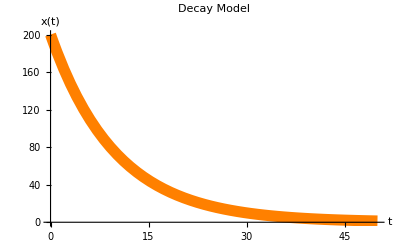

```mathematica
Plot[Sol1,{t,0,50}, PlotStyle-> {Orange, Thickness[0.02]}, PlotLabel-> "Decay Model", AxesLabel -> {t, x[t]}]
```

```mathematica
x[3] = Evaluate[Sol1/.{t-> 3}]
```

148.164

```mathematica
Conclusion: Hence, grams left after 3 years will be 148.164.
```

```mathematica
ClearAll
```

ClearAll

```mathematica
Example - 5
Using the same element as Example -4, if a particular sample of the element decays to 50grams after 5 years, how big was the original sample?
```

```mathematica
k = 10% = 0.1, t = 5, x(t) = 50, x[0]=?
```

```mathematica
Clear[t,k,x]
```

```mathematica
Sol = DSolve[x'[t] == -k*x[t], x[t], t]
```

{{x[t]→ⅇ^(-k t) C[1]}}

```mathematica
Sol1 = Evaluate[x[t]/.Sol[[1]]/.{k-> .1, C[1]-> Subscript[x, o], t-> 5}]
```

0.606531 x_o

```mathematica
Sol2 = Solve[Sol1 == 50, Subscript[x, o]]
```

{{x_o→82.4361}}

```mathematica
Sol3 = Subscript[x, o]/.Sol2[[1]]
```

82.4361

```mathematica
Sol4 = x[t]/.Sol[[1]]/.{k-> 0.1, C[1] -> Sol3}
```

82.4361 ⅇ^(-0.1 t)

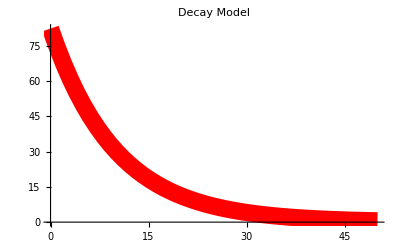

```mathematica
Plot[Sol4, {t,0,50}, PlotStyle-> {Red, Thickness[0.031]}, PlotLabel -> "Decay Model"]
```

```mathematica
Conclusion: Hence, original sample was 82.4361 grams.
```

```mathematica
Example - 6
Suppose that a certain radioactive isotope has an annual decay rate of 5%. How many years will it take for a 100 gram sample to decay to 40 grams?
```

```mathematica
Here, k = 5% = 0.05, x(0) = 100, x(t) = 40, t= ?
```

```mathematica
Clear[t,k,x]
```

```mathematica
Sol=DSolve[x'[t]==-k*x[t],x[t],t]
```

{{x[t]→ⅇ^(-k t) C[1]}}

```mathematica
Sol1=Evaluate[x[t]/.Sol[[1]]/.{k-> .05,C[1]-> 100}]
```

100 ⅇ^(-0.05 t)

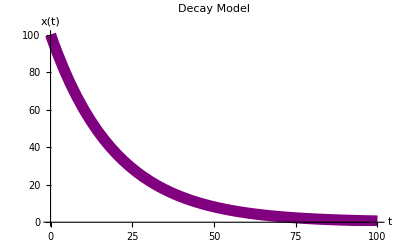

```mathematica
Plot[Sol1,{t,0,100},PlotStyle-> {Purple,Thickness[0.02]},PlotLabel-> "Decay Model",AxesLabel-> {t,x[t]}]
```

```mathematica
Solve[Sol1==40,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→18.3258}}

```mathematica
Conclusion : Hence it will take 18.3258 years for 100gram sample to decay to 40 grams.
```

```mathematica
Example - 7
Using the same element as in Example - 6, what is the half life of the element?
Here, k = 5% = 0.05, x(0) = 100, x(t) = 40, t= ?
```

```mathematica
Sol = DSolve[x'[t] == -k*x[t], x[t], t]
```

{{x[t]→ⅇ^(-k t) C[1]}}

```mathematica
Sol1 = Evaluate[x[t]/.Sol[[1]]/.{k-> 0.05,C[1]-> 100}]
```

100 ⅇ^(-0.05 t)

```mathematica
Solve[Sol1==50,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→13.8629}}

```mathematica
Conclusion: Hence, half-life of radioactive isotope is 13.8629 years.
```